## PHAS2443 Mini-project Decision-making in Committees Hayk Khachatryan - 15013904 Logbook

## 24/02/2018

```mathematica
<<IGraphM`
```

IGraph/M 0.3.97.2 (February 5, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
IGDocumentation[]
```

```mathematica
Clear[modeler]

modeler[n_, {k_, {h0_, h1_}, e_}] := 
(* 
	Implementation of Parkinson's Law  for decision-making in committees;
	

	inputs:
;	
		n: committee size (n ∈ ℕ);

		{k, h, e}: model parameters;
			k: connectivity (number of undirected links between nodes) (k ∈ ℕ);
			h: threshold (h ∈ [0.5, 1]);
			e: rewiring probability (e ∈ [0, 1]);

	outputs:
;
		graph probably
*)

Module[
{},

]


modeler::usage = "D[n, {k, h, e}] gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute"
```

D[N, {k, h, e}] gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute

```mathematica
dissensus[n_, sf_, si_] := 
HeavisideTheta[1-Max[sf, n-sf]/n]
```

```mathematica
dissensus[15,3,10]
```

1

```mathematica
Graph[{1 <-> 2, 2<-> 3, 2<-> 4, 1<-> 4}]
```

-Graphics-

### Need to implement the majority update func

```mathematica
Clear[majority]

majority[h_,list_]:=
(*
	Returns 1 if a majority above the threshold 'h' is reached;
	Returns 0 if no majority above the threshold 'h' is reached;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{},

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2) and returns True if at least a majority above the threshold h are agree  *)
{
Round[h Length[list]],
Length[list]
},
Length[list]
] @@ list

]

]

BooleanConvert[majority[0.6, {a,b,c,d,e}]]
```

(a&&b&&c)||(a&&b&&d)||(a&&b&&e)||(a&&c&&d)||(a&&c&&e)||(a&&d&&e)||(b&&c&&d)||(b&&c&&e)||(b&&d&&e)||(c&&d&&e)

Majority fails to return True for a majority of state 0. This is because BooleanCountingFunction creates a logical statement comparing the elements in the list to each other to see if they’re the same. For a list { a, b, c, d } with h = 0.75, it checks

```mathematica
( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d )
```

(a&&b&&c)||(a&&b&&d)||(b&&c&&d)

While this works when the majority has a state of 1, it fails to work when the majority has a state of 0 (as 0 ∧ 0 ∧ 0 = 0)

```mathematica
Simplify[( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d ) /. {a -> 1, b -> 1, c-> 1, d -> 0}]
Simplify[( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d ) /. {a -> 1, b -> 0, c-> 0, d -> 0}]
```

True

False

```mathematica
Clear[swaps]

swaps[h_, list_, 0] :=
If[majority[h,list],1,0]
swaps[h_,list_, 1] :=
If[majority[h,list], 0, 1]
swaps[h_, list_, e] :=
If[majority[h,list],1,0]
```

## 25/02/2018

Working on a majority function that takes into account  0 ∧ 0 = 0

```mathematica
Clear[majority]

majority[h_,list_]:=
(*
	Returns 1 if a majority above the threshold 'h' is reached;
	Returns 0 if no majority above the threshold 'h' is reached;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{},

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2) and returns True if at least a majority above the threshold h agree *)
{
Round[h Length[list]],
Length[list]
},
Length[list]
] @@ list

]

]

BooleanConvert[majority[0.6, {a,b,c,d,e}]]
```

(a&&b&&c)||(a&&b&&d)||(a&&b&&e)||(a&&c&&d)||(a&&c&&e)||(a&&d&&e)||(b&&c&&d)||(b&&c&&e)||(b&&d&&e)||(c&&d&&e)

Idea: pass dummy list to BooleanCountingFunction (to get disjunctive form) then swap the elements in the dummy list with our list

```mathematica
h = 0.6
list = {False, False, False, False, True}
l = {0,0,0,0,1}
ab = {a,b,c,d,e}

fdsa = BooleanConvert[
BooleanCountingFunction[
{
Round[h Length[list]],
Length[list]
},
Length[list]
] @@ Table[bdd i, {i, 1, Length[l]}] ] 


(* then swap the bdd's back with rules *)
```

0.6

{False,False,False,False,True}

{0,0,0,0,1}

{a,b,c,d,e}

(bdd&&2 bdd&&3 bdd)||(bdd&&2 bdd&&4 bdd)||(bdd&&2 bdd&&5 bdd)||(bdd&&3 bdd&&4 bdd)||(bdd&&3 bdd&&5 bdd)||(bdd&&4 bdd&&5 bdd)||(2 bdd&&3 bdd&&4 bdd)||(2 bdd&&3 bdd&&5 bdd)||(2 bdd&&4 bdd&&5 bdd)||(3 bdd&&4 bdd&&5 bdd)

Small break from figuring out majority, playing around with cellular automata

(0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

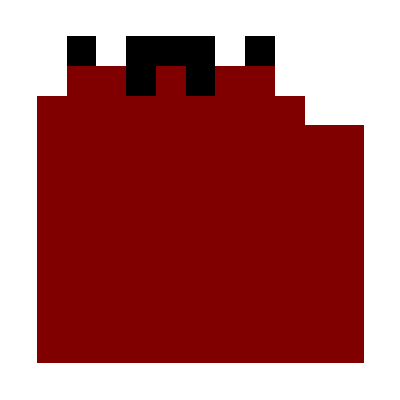

```mathematica
Clear[up]

up[lst_,t_]:=BooleanConvert[majority[0.8,lst]]


With[
{
init={0,1,0,1,1,1,0,1,0,0,0},
nsteps=10,
r=2
},
res=CellularAutomaton[{up,{},r},init,nsteps]
];
MatrixForm[res] //. {0 -> False, 1-> True} //. {False -> 0, True -> 1}

ArrayPlot[res]
```

## 26/02/2018

Finish implementing dummy list

```mathematica
h = 0.6
list = {False, False, False, False, True}
l = {0,0,0,0,1}
abList =  Table[bdd i, {i, 1, Length[l]}] 

fdsa = BooleanConvert[
BooleanCountingFunction[
{
Round[h Length[list]],
Length[list]
},
Length[list]
] @@ abList]


fdsa //. Table[abList[[i]] -> l[[i]], {i, 1, Length[l]}] //. {And -> Equal}
```

0.6

{False,False,False,False,True}

{0,0,0,0,1}

{bdd,2 bdd,3 bdd,4 bdd,5 bdd}

(bdd&&2 bdd&&3 bdd)||(bdd&&2 bdd&&4 bdd)||(bdd&&2 bdd&&5 bdd)||(bdd&&3 bdd&&4 bdd)||(bdd&&3 bdd&&5 bdd)||(bdd&&4 bdd&&5 bdd)||(2 bdd&&3 bdd&&4 bdd)||(2 bdd&&3 bdd&&5 bdd)||(2 bdd&&4 bdd&&5 bdd)||(3 bdd&&4 bdd&&5 bdd)

True

Success! Now to implement it into majority[h, list]

```mathematica
Clear[majority, stringer]

stringer[i_] := ToString[ab]<>ToString[i] (* creates a value "abi" for dummy variables in majority *)

majority[ h_, list_]:= 
(*
	Returns True if a majority above the threshold 'h' is reached in list;
	Returns False if no majority above the threshold 'h' is reached in list;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{
ab, swaps
},

ab = Table[stringer[i], {i, 1, Length[list]}];  (* dummy list of {ab1, ab2, ab3, ..., abN} where N is the length of list *)
swaps =  Table[ab[[i]] -> list[[i]], {i, 1, Length[list]}]; (* creates a list of transformations {ab1 -> list[1], ab2 -> list[2], ..., abN -> list[N]} to swap back after BooleanCountingFunction *)

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2, ∧ is later swapped with ==) and returns True if at least a majority above the threshold h are agree  *)
{
Round[h Length[list]],
Length[list]
},
Length[list]
] @@ ab

] //. swaps //. And -> Equal
]

RepeatedTiming[majority[0.95, {0,0,0,0,0,0,0,0,0,1}]]
```

{0.0003,False}

## 27/02/2018

I wonder if using Dispatch to package the rules would increase performance

```mathematica
Clear[dispatchedMajority]

dispatchedMajority[ h_, list_]:= 
(*
	Returns True if a majority above the threshold 'h' is reached in list;
	Returns False if no majority above the threshold 'h' is reached in list;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{
ab, swaps
},

ab = Table[stringer[i], {i, 1, Length[list]}];  (* dummy list of {ab1, ab2, ab3, ..., abN} where N is the length of list *)
swaps =  Dispatch[Table[ab[[i]] -> list[[i]], {i, 1, Length[list]}]]; (* creates a list of transformations {ab1 -> list[1], ab2 -> list[2], ..., abN -> list[N]} to swap back after BooleanCountingFunction *)

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2, ∧ is later swapped with ==) and returns True if at least a majority above the threshold h are agree  *)
{
Round[h Length[list]],
Length[list]
},
Length[list]
] @@ ab

] //. swaps //. And -> Equal
]
```

```mathematica
tt := Catenate[{Flatten[Table[{1,0}, i]]}]

(*dispatched = Table[
RepeatedTiming[
dispatchedMajority[
0.6,
tt]
],
{i, 0, 12}
];

notDispatched = Table[RepeatedTiming[
majority[
0.6,
tt]],
{i, 0, 12}];

ListPlot[{Transpose[notDispatched][[1]],Transpose[dispatched][[1]] }, Joined ->  True, PlotLabels->{ "Not Dispatched","Dispatched"}, PlotRange->All, AxesLabel->{"Number of elements in list", "seconds"}] *)
```

```mathematica
ListPlot[{Transpose[notDispatched][[1]],Transpose[dispatched][[1]] }, Joined ->  True, PlotLabels->{ "Not Dispatched","Dispatched"}, PlotRange->All, AxesLabel->{"Number of elements in list", "seconds"}]
```

First::nofirst: {} has zero length and no first element.

Part::pkspec1: The expression -1+First[{}] cannot be used as a part specification.

Last::nolast: {} has zero length and no last element.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::nmtx: The first two levels of {1} cannot be transposed.

Set::shape: Lists {Charting`CommonDump`lastpoints$5817,Charting`CommonDump`labels$5817} and … are not the same shape.

Part::pkspec1: The expression Transpose[{1}] cannot be used as a part specification.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Part::pkspec1: The expression -1+First[{}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

-Graphics-

```mathematica
Last[Transpose[notDispatched][[1]]] / Last[Transpose[dispatched][[1]]]
```

Last::normal: Nonatomic expression expected at position 1 in Last[notDispatched].

Last::normal: Nonatomic expression expected at position 1 in Last[dispatched].

Last[notDispatched]/Last[dispatched]

As we can see, using Dispatch in the majority function with lists with more than 10 elements is ~2 times faster. So let’s redefine majority to use Dispatch

```mathematica
Clear[majority]

majority[ h_, list_]:= 
(*
	Returns True if a majority above the threshold 'h' is reached in list;
	Returns False if no majority above the threshold 'h' is reached in list;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{
ab, swaps
},

ab = Table[stringer[i], {i, 1, Length[list]}];  (* dummy list of {ab1, ab2, ab3, ..., abN} where N is the length of list *)
swaps =  Dispatch[Table[ab[[i]] -> list[[i]], {i, 1, Length[list]}]]; (* creates a list of transformations {ab1 -> list[1], ab2 -> list[2], ..., abN -> list[N]} to swap back after BooleanCountingFunction *)

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2, ∧ is later swapped with ==) and returns True if at least a majority above the threshold h are agree  *)
{
Round[h Length[list]],
Length[list]
},
Length[list]
] @@ ab

] //. swaps //. And -> Equal
]
```

Figure out what the majority is, and thus whether the state of a member changes.

```mathematica
Clear[adopts]

adopts[h_, list_] := 
(* Checks if there is a majority in list above threshold h, then returns the majority state *)
If[
majority[h, list],
Commonest[list][[1]],
False]

adopts[0.8, {0,0,1,1,1}]
adopts[0.8, {0,1,1,1,1}]
adopts[0.8, {0,0,0,0,1}]
```

False

1

0

Try implementing with cellular automata

```mathematica
With[
{
sample = RandomSample[Catenate[Table[{0,1}, {i, 1, 50}]], 50],
steps = 10,
r = 4,
h = 0.6
},
res = 
CellularAutomaton[
{
adopts[h,#]&,
{},
r
},
sample,
steps]];

ArrayPlot[res]
```

-Graphics-

As we can see, group think is beginning to emerge

```mathematica
RandomGraph[{15,105}]
```

-Graphics-

```mathematica
NearestNeighborGraph[Range[15], 8]
```

-Graphics-

```mathematica
NearestNeighborGraph[RandomChoice[{True,False},{50,3}],DistanceFunction->JaccardDissimilarity]
```

-Graphics-

```mathematica
RelationGraph[#1<6&&#2≥6&,{1,2,3,4,5,6,7,8}]
```

-Graphics-

## 28/02/2018

Implementing Small-World networks using IGraph/M 
(from https://mathematica.stackexchange.com/questions/106122/small-world-network-on-a-square-grid)

```mathematica
<<IGraphM`
```

IGraph/M 0.3.97.2 (February 5, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
g  = GridGraph[{5,5}];
coords = GraphEmbedding[g];
Graph[IGRewireEdges[g, 0.3], VertexCoordinates->coords]
```

-Graphics-

```mathematica
?IGMakeLattice
```

IGMakeLattice[{d1, d2, …}] generates a lattice graph of the given dimensions.

Need to add more neighbors

```mathematica
g = IGMakeLattice[{8}, Radius ->2 , Periodic->True]
g2 = IGRewireEdges[g, 0.3]
```

-Graphics-

-Graphics-

Turn into func and assign values to the vertices

```mathematica
Clear[grapher]

grapher[n_, k_, h_, e_] :=
Module[
{r, states, graph, rewiredGraph},

r = Round[k/2];

states = Table[i -> ToString[RandomInteger[{0,1}]], {i, 1, n}];
graph = IGMakeLattice[{n}, Radius ->r, Periodic->True, VertexLabels-> states] 



(*rewiredGraph = IGRewireEdges[graph, e]*)

(*Show[graph];*)
]

grapher[9, 4, 1, 0.3]
```

-Graphics-

Use IGRandomWalk to randomly select the node to update

## 01/03/2018

Looking through example netwrok graphs to figure out exactly how vertices and their properties work

```mathematica
ExampleData["NetworkGraph"]
```

{{NetworkGraph,AmericanCollegeFootball},{NetworkGraph,AskOpinionRecall},{NetworkGraph,AskOpinionRecognition},{NetworkGraph,AstrophysicsCollaborations},{NetworkGraph,BeAskedOpinionRecall},{NetworkGraph,BeAskedOpinionRecognition},{NetworkGraph,BipartiteDiseasomeNetwork},{NetworkGraph,Brock2001},{NetworkGraph,Brock2002},{NetworkGraph,Brock2003},{NetworkGraph,Brock2004},{NetworkGraph,Brock4001},{NetworkGraph,Brock4002},{NetworkGraph,Brock4003},{NetworkGraph,Brock4004},{NetworkGraph,Brock8001},{NetworkGraph,Brock8002},{NetworkGraph,Brock8003},{NetworkGraph,Brock8004},{NetworkGraph,BuddingYeast},{NetworkGraph,CellOntology},{NetworkGraph,CFat2001},{NetworkGraph,CFat2002},{NetworkGraph,CFat2005},{NetworkGraph,CFat5001},{NetworkGraph,CFat50010},{NetworkGraph,CFat5002},{NetworkGraph,CFat5005},{NetworkGraph,CoauthorshipsInNetworkScience},{NetworkGraph,CondensedMatterCollaborations},{NetworkGraph,CondensedMatterCollaborations2003},{NetworkGraph,CondensedMatterCollaborations2005},{NetworkGraph,DavisSouthernWomen},{NetworkGraph,DiscussionRecall},{NetworkGraph,DiscussionRecognition},{NetworkGraph,DiseaseGeneNetwork},{NetworkGraph,DolphinSocialNetwork},{NetworkGraph,EastAfricaEmbassyAttacks},{NetworkGraph,EmailListMathGroup},{NetworkGraph,EuclidElements},{NetworkGraph,EurovisionVotes},{NetworkGraph,ExpandedAbortion},{NetworkGraph,ExpandedComputationalComplexity},{NetworkGraph,ExpandedComputationalGeometry},{NetworkGraph,ExpandedDeathPenalty},{NetworkGraph,ExpandedGenetic},{NetworkGraph,ExpandedGunControl},{NetworkGraph,ExpandedMovies},{NetworkGraph,ExpandedNetCensorship},{NetworkGraph,FamilyGathering},{NetworkGraph,FlorentineFamilies},{NetworkGraph,FreeAssociationNormsAppendixA},{NetworkGraph,Friendship},{NetworkGraph,Hamming102},{NetworkGraph,Hamming104},{NetworkGraph,Hamming62},{NetworkGraph,Hamming64},{NetworkGraph,Hamming82},{NetworkGraph,Hamming84},{NetworkGraph,HighEnergyPhysicsPhenomenology},{NetworkGraph,HighEnergyPhysicsTheory},{NetworkGraph,HighEnergyTheoryCollaborations},{NetworkGraph,HumanDiseaseNetwork},{NetworkGraph,Internet},{NetworkGraph,JazzMusicians},{NetworkGraph,Johnson1624},{NetworkGraph,Johnson3224},{NetworkGraph,Johnson824},{NetworkGraph,Johnson844},{NetworkGraph,Keller4},{NetworkGraph,Keller5},{NetworkGraph,Keller6},{NetworkGraph,LesMiserables},{NetworkGraph,MannA27},{NetworkGraph,MannA45},{NetworkGraph,MannA81},{NetworkGraph,MannA9},{NetworkGraph,MarvelUniverseSocialGraph},{NetworkGraph,MetabolicNetworkActinobacillusActinomycetemcomitans},{NetworkGraph,MetabolicNetworkAeropyrumPernix},{NetworkGraph,MetabolicNetworkAquifexAeolicus},{NetworkGraph,MetabolicNetworkArabidopsisThaliana},{NetworkGraph,MetabolicNetworkArchaeoglobusFulgidus},{NetworkGraph,MetabolicNetworkBacillusSubtilis},{NetworkGraph,MetabolicNetworkBorreliaBurgdorferi},{NetworkGraph,MetabolicNetworkCaenorhabditisElegans},{NetworkGraph,MetabolicNetworkCampylobacterJejuni},{NetworkGraph,MetabolicNetworkChlamydiaPneumoniae},{NetworkGraph,MetabolicNetworkChlamydiaTrachomatis},{NetworkGraph,MetabolicNetworkChlorobiumTepidum},{NetworkGraph,MetabolicNetworkClostridiumAcetobutylicum},{NetworkGraph,MetabolicNetworkDeinococcusRadiodurans},{NetworkGraph,MetabolicNetworkEmericellaNidulans},{NetworkGraph,MetabolicNetworkEnterococcusFaecalis},{NetworkGraph,MetabolicNetworkEscherichiaColi},{NetworkGraph,MetabolicNetworkHaemophilusInfluenzae},{NetworkGraph,MetabolicNetworkHelicobacterPylori},{NetworkGraph,MetabolicNetworkMethanobacteriumThermoautotrophicum},{NetworkGraph,MetabolicNetworkMethanococcusJannaschii},{NetworkGraph,MetabolicNetworkMycobacteriumBovis},{NetworkGraph,MetabolicNetworkMycobacteriumLeprae},{NetworkGraph,MetabolicNetworkMycobacteriumTuberculosis},{NetworkGraph,MetabolicNetworkMycoplasmaGenitalium},{NetworkGraph,MetabolicNetworkMycoplasmaPneumoniae},{NetworkGraph,MetabolicNetworkNeisseriaGonorrhoeae},{NetworkGraph,MetabolicNetworkNeisseriaMeningitidis},{NetworkGraph,MetabolicNetworkOryzaSativa},{NetworkGraph,MetabolicNetworkPorphyromonasGingivalis},{NetworkGraph,MetabolicNetworkPseudomonasAeruginosa},{NetworkGraph,MetabolicNetworkPyrococcusFuriosus},{NetworkGraph,MetabolicNetworkPyrococcusHorikoshii},{NetworkGraph,MetabolicNetworkRhodobacterCapsulatus},{NetworkGraph,MetabolicNetworkRickettsiaProwazekii},{NetworkGraph,MetabolicNetworkSaccharomycesCerevisiae},{NetworkGraph,MetabolicNetworkSalmonellaTyphi},{NetworkGraph,MetabolicNetworkStreptococcusPneumoniae},{NetworkGraph,MetabolicNetworkStreptococcusPyogenes},{NetworkGraph,MetabolicNetworkSynechocystisSp},{NetworkGraph,MetabolicNetworkThermotogaMaritima},{NetworkGraph,MetabolicNetworkTreponemaPallidum},{NetworkGraph,MetabolicNetworkYersiniaPestis},{NetworkGraph,NationalHockeyLeague},{NetworkGraph,OnlineSocialNetwork},{NetworkGraph,PerlModuleAuthors},{NetworkGraph,PGPNetwork},{NetworkGraph,PHat10001},{NetworkGraph,PHat10002},{NetworkGraph,PHat10003},{NetworkGraph,PHat15001},{NetworkGraph,PHat15002},{NetworkGraph,PHat15003},{NetworkGraph,PHat3001},{NetworkGraph,PHat3002},{NetworkGraph,PHat3003},{NetworkGraph,PHat5001},{NetworkGraph,PHat5002},{NetworkGraph,PHat5003},{NetworkGraph,PHat7001},{NetworkGraph,PHat7002},{NetworkGraph,PHat7003},{NetworkGraph,PoliticalBlogs},{NetworkGraph,PowerGrid},{NetworkGraph,ProteinInteraction},{NetworkGraph,RefinedAbortion},{NetworkGraph,RefinedComputationalComplexity},{NetworkGraph,RefinedComputationalGeometry},{NetworkGraph,RefinedDeathPenalty},{NetworkGraph,RefinedGenetic},{NetworkGraph,RefinedGunControl},{NetworkGraph,RefinedMovies},{NetworkGraph,RefinedNetCensorship},{NetworkGraph,RegularAbortion},{NetworkGraph,RegularComputationalComplexity},{NetworkGraph,RegularComputationalGeometry},{NetworkGraph,RegularDeathPenalty},{NetworkGraph,RegularGenetic},{NetworkGraph,RegularGunControl},{NetworkGraph,RegularMovies},{NetworkGraph,RegularNetCensorship},{NetworkGraph,San1000},{NetworkGraph,San200071},{NetworkGraph,San200072},{NetworkGraph,San200091},{NetworkGraph,San200092},{NetworkGraph,San200093},{NetworkGraph,San400051},{NetworkGraph,San400071},{NetworkGraph,San400072},{NetworkGraph,San400073},{NetworkGraph,San400091},{NetworkGraph,Sanr20007},{NetworkGraph,Sanr20009},{NetworkGraph,Sanr40005},{NetworkGraph,Sanr40007},{NetworkGraph,September11Terrorists},{NetworkGraph,SimpleFoodWeb},{NetworkGraph,SloveneParliamentaryParties},{NetworkGraph,TaggedTestImages},{NetworkGraph,URVEmailNetwork},{NetworkGraph,USPoliticsBooks},{NetworkGraph,WholeNetworkActinobacillusActinomycetemcomitans},{NetworkGraph,WholeNetworkAeropyrumPernix},{NetworkGraph,WholeNetworkAquifexAeolicus},{NetworkGraph,WholeNetworkArabidopsisThaliana},{NetworkGraph,WholeNetworkArchaeoglobusFulgidus},{NetworkGraph,WholeNetworkBacillusSubtilis},{NetworkGraph,WholeNetworkBorreliaBurgdorferi},{NetworkGraph,WholeNetworkCaenorhabditisElegans},{NetworkGraph,WholeNetworkCampylobacterJejuni},{NetworkGraph,WholeNetworkChlamydiaPneumoniae},{NetworkGraph,WholeNetworkChlamydiaTrachomatis},{NetworkGraph,WholeNetworkChlorobiumTepidum},{NetworkGraph,WholeNetworkClostridiumAcetobutylicum},{NetworkGraph,WholeNetworkDeinococcusRadiodurans},{NetworkGraph,WholeNetworkEmericellaNidulans},{NetworkGraph,WholeNetworkEnterococcusFaecalis},{NetworkGraph,WholeNetworkEscherichiaColi},{NetworkGraph,WholeNetworkHaemophilusInfluenzae},{NetworkGraph,WholeNetworkHelicobacterPylori},{NetworkGraph,WholeNetworkMethanobacteriumThermoautotrophicum},{NetworkGraph,WholeNetworkMethanococcusJannaschii},{NetworkGraph,WholeNetworkMycobacteriumBovis},{NetworkGraph,WholeNetworkMycobacteriumLeprae},{NetworkGraph,WholeNetworkMycobacteriumTuberculosis},{NetworkGraph,WholeNetworkMycoplasmaGenitalium},{NetworkGraph,WholeNetworkMycoplasmaPneumoniae},{NetworkGraph,WholeNetworkNeisseriaGonorrhoeae},{NetworkGraph,WholeNetworkNeisseriaMeningitidis},{NetworkGraph,WholeNetworkOryzaSativa},{NetworkGraph,WholeNetworkPorphyromonasGingivalis},{NetworkGraph,WholeNetworkPseudomonasAeruginosa},{NetworkGraph,WholeNetworkPyrococcusFuriosus},{NetworkGraph,WholeNetworkPyrococcusHorikoshii},{NetworkGraph,WholeNetworkRhodobacterCapsulatus},{NetworkGraph,WholeNetworkRickettsiaProwazekii},{NetworkGraph,WholeNetworkSaccharomycesCerevisiae},{NetworkGraph,WholeNetworkSalmonellaTyphi},{NetworkGraph,WholeNetworkStreptococcusPneumoniae},{NetworkGraph,WholeNetworkStreptococcusPyogenes},{NetworkGraph,WholeNetworkSynechocystisSp},{NetworkGraph,WholeNetworkThermotogaMaritima},{NetworkGraph,WholeNetworkTreponemaPallidum},{NetworkGraph,WholeNetworkYersiniaPestis},{NetworkGraph,WikiVote},{NetworkGraph,WordAdjacencies},{NetworkGraph,WorldCup1988},{NetworkGraph,WorldWideWeb},{NetworkGraph,ZacharyKarateClub}}

CondensedMatterCollaborations has properties other than the usual {VertexCoordinates,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

```mathematica
b =Graph[ExampleData[{"NetworkGraph","EastAfricaEmbassyAttacks"}],ImageSize->Medium]
IGVertexPropertyList[b]
```

-Graphics-

{FullName,Group,VertexCoordinates,VertexLabels,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

Try changing one of the “Name”s

```mathematica
IGVertexProp["FullName"][b][[1]]
PropertyValue[{b,"Osama"}, "FullName"] = "Hayk Khachatryan"
IGVertexProp["FullName"][b][[1]]
```

Osama Bin Laden

Hayk Khachatryan

Hayk Khachatryan

Try creating a new property

```mathematica
IGVertexProp["State"][b][[1]]
PropertyValue[{b,"Osama"}, "State"] = "0"
IGVertexProp["State"][b][[1]]

PropertyValue[{b,"Osama"}, "State"] = "1"
IGVertexProp["State"][b][[1]]
```

Missing[Nonexistent]

0

0

1

1

Success!
Now implement into grapher

```mathematica
Clear[latticer]

latticer[n_, r_]:=
(* Created a 1D periodic lattice with radius r *)
IGMakeLattice[{n},Radius ->r,Periodic->True]

latticer[9,2]
```

-Graphics-

https://mathematica.stackexchange.com/questions/143601/get-or-set-vertex-properties-for-all-graph-vertices-at-once

```mathematica
Clear[setVertexProp]

setVertexProp[g_,prop_,vals_]:=
(*
	Sets the property prop of the vertices in g to vals;

	input;
		g: graph;
		prop: property of vertex;
		vals: a list of values;

	output;
		a graph
*)
Module[
{h=g,vl=VertexList@g},
Do[
PropertyValue[
{
h,
vl[[i]]
},
prop
]=vals[[i]],
{i,Length@vl}
];
Return@h]
```

```mathematica
Clear[grapher]

grapher[n_, k_, e_] :=
(*
	Creates a graph of n members with random states (0/1);
	linked to their k nearest neighbors;
	The links are then each rewired with probability e;

	input;
		n: number of members;
		k: degrees of vertex;
		e: probablity of rewiring;

	outputs;
		a graph
*)

Module[
{r, states, graph,g1},

r = (* radius of lattice *)
Round[k/2];

states = (* a list of random states between 0 <-> 1 *)
Table[RandomInteger[1], n];

graph=  

setVertexProp[ (* sets the "State"s and VertexLabels to 'states' *)

IGRewireEdges[ (* rewires the graph with probability e *)
latticer[n,r],(* creates a graph of n members with radius r *)
e
],  

{"State", VertexLabels}, 
states

]
]
```

```mathematica
h =Table[grapher[35,4,0.3], 35];
g = grapher[25,8,0.3]
ArrayPlot[IGVertexProp["State"] /@ h]
```

-Graphics-

-Graphics-

```mathematica
j = grapher[9, 4, 0.3]
IGRandomWalk[j, 1, 10]
```

-Graphics-

{1,7,1,5,8,1,4,9,5,9}

## 02/03/2018

```mathematica
j
NeighborhoodGraph[j,2]
AdjacencyList[j, 2]
```

-Graphics-

-Graphics-

{1,3,6,7}

Use AdjacencyList to select linked nodes of a node

```mathematica
vList =VertexList[j]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
RandomSample[vList, Length[vList]]
```

{8,6,3,4,1,5,9,2,7}

Use RandomSample to randomize the list of vertices then map over the majority choosing function through that.

```mathematica
PropertyValue[{j, #}, "State"]& /@ AdjacencyList[j,2]
```

{0,0,0,1}

```mathematica
AdjacencyList[j, #] & /@  vList
```

{{2,4,5,7,8},{1,3,6,7},{2,5,6},{1,6,9},{1,3,6,8,9},{2,3,4,5,8,9},{1,2,8},{1,5,6,7},{4,5,6}}

```mathematica
Clear[associatedAdjacencyLister]

associatedAdjacencyLister[g_] :=
AssociationThread[
Range[1, Length[VertexList[g]]],
AdjacencyList[g,#] & /@ VertexList[g]]
```

```mathematica
associatedAdjacencyLister[j]
```

<|1→{2,4,5,7,8},2→{1,3,6,7},3→{2,5,6},4→{1,6,9},5→{1,3,6,8,9},6→{2,3,4,5,8,9},7→{1,2,8},8→{1,5,6,7},9→{4,5,6}|>

```mathematica
RandomSample[associatedAdjacencyLister[j], Length[associatedAdjacencyLister[j]]]
```

<|8→{1,5,6,7},5→{1,3,6,8,9},2→{1,3,6,7},3→{2,5,6},1→{2,4,5,7,8},7→{1,2,8},4→{1,6,9},6→{2,3,4,5,8,9},9→{4,5,6}|>

```mathematica
Clear[randomALister]

randomALister[list_]:=
RandomSample[list, Length[list]]
```

```mathematica
list = randomALister[associatedAdjacencyLister[j]]
```

<|5→{1,3,6,8,9},3→{2,5,6},7→{1,2,8},2→{1,3,6,7},9→{4,5,6},6→{2,3,4,5,8,9},4→{1,6,9},8→{1,5,6,7},1→{2,4,5,7,8}|>

```mathematica
list[9]
```

{4,5,6}

Generate the states of nodes adjacent to the first element of randomALister and calculated the (majority) updated state of that. Then move down the randomALister list repeating this. This is to preserve the changes

```mathematica
Clear[propertyChecker]

propertyChecker[g_, list_]:=
PropertyValue[{g, #}, "State"] & /@ list
```

```mathematica
propertyChecker[j, list]
```

<|5→PropertyValue[{-Graphics-,{1,3,6,8,9}},State],3→PropertyValue[{-Graphics-,{2,5,6}},State],7→PropertyValue[{-Graphics-,{1,2,8}},State],2→PropertyValue[{-Graphics-,{1,3,6,7}},State],9→PropertyValue[{-Graphics-,{4,5,6}},State],6→PropertyValue[{-Graphics-,{2,3,4,5,8,9}},State],4→PropertyValue[{-Graphics-,{1,6,9}},State],8→PropertyValue[{-Graphics-,{1,5,6,7}},State],1→PropertyValue[{-Graphics-,{2,4,5,7,8}},State]|>

## 03/03/2018

Add another pure mapping function to pull out specific vertices from vList instead of passing a list of vertices to PropertyValue

```mathematica
Clear[propertyChecker]

propertyChecker[g_, list_, property_]:=
PropertyValue[{g, #}, property] & /@ # & /@ list
```

```mathematica
list = propertyChecker[j, randomALister[associatedAdjacencyLister[j]], "State"]
```

<|9→{0,1,0},5→{0,0,0,1,0},2→{0,0,0,1},1→{1,0,1,1,1},4→{0,0,0},8→{0,1,0,1},7→{0,1,1},3→{1,1,0},6→{1,0,0,1,1,0}|>

Success! Now to figure out implementing majority[h, list] with this (and calculating the property values of neighboring vertices after the previous majority update)

First let’s create a function with majority that returns the new state, then figure out how to implement it inbetween steps in propertyChecker

```mathematica
Clear[newState]

newState[h_, list_] :=
0 /;( majority[h,list] ∧ (Commonest[list][[1]] == 0))

newState[h_,list_] :=
1 /; (majority[h, list] ∧ (Commonest[list][[1]] == 1))

newState[0.6, {0,0,0,1,1}]
newState[0.6, {0,0,1,1,1}]
```

0

1

```mathematica
newState[0.6, #] & /@ list
```

<|9→0,5→0,2→0,1→1,4→0,8→0,7→1,3→1,6→newState[0.6,{1,0,0,1,1,0}]|>

As we can see this generates an association list of VertexLabels and the new states. Though we can see our newState function doesn’t work correctly for a list of 2 values. Also as this generates the new states of a static list of vertices, it doesn’t take into account that as you go along the list assigning new values to vertices, further vertex calculations will be carried out with old vertex properties instead of the newly assigned ones.

## 07/03/2018

```mathematica
Clear[heldPropertyChecker]

heldPropertyChecker[g_, list_, property_]:=
Hold[PropertyValue[{g, #}, property]] & /@ # & /@ list
```

```mathematica
heldList = heldPropertyChecker[j, randomALister[associatedAdjacencyLister[j]], "State"]
```

<|6→{Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,8},State]],Hold[PropertyValue[{-Graphics-,9},State]]},3→{Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,6},State]]},9→{Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,6},State]]},4→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,9},State]]},7→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,8},State]]},5→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,8},State]],Hold[PropertyValue[{-Graphics-,9},State]]},1→{Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,7},State]],Hold[PropertyValue[{-Graphics-,8},State]]},8→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,7},State]]},2→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,7},State]]}|>

```mathematica
ReleaseHold[#] & /@ heldList
```

<|6→{1,0,0,1,1,0},3→{1,1,0},9→{0,1,0},4→{0,0,0},7→{0,1,1},5→{0,0,0,1,0},1→{1,0,1,1,1},8→{0,1,0,1},2→{0,0,0,1}|>

```mathematica
newState[0.6, ReleaseHold[#]] &/@ heldList
```

<|6→newState[0.6,{1,0,0,1,1,0}],3→1,9→0,4→0,7→1,5→0,1→1,8→0,2→0|>

Use new grapher func that doesn’t change vertex labels so that we can hand calculate some of these operations to verify them

```mathematica
Clear[grapher2]

grapher2[n_, k_, e_] :=
(*
	Creates a graph of n members with random states (0/1);
	linked to their k nearest neighbors;
	The links are then each rewired with probability e;

	input;
		n: number of members;
		k: degrees of vertex;
		e: probablity of rewiring;

	outputs;
		a graph
*)

Module[
{r, states, graph,g1},

r = (* radius of lattice *)
Round[k/2];

states = (* a list of random states between 0 <-> 1 *)
Table[RandomInteger[1], n];

graph=  

setVertexProp[ (* sets the "State"s and VertexLabels to 'states' *)

IGRewireEdges[ (* rewires the graph with probability e *)
latticer[n,r],(* creates a graph of n members with radius r *)
e
],  

"State", 
states

]
]
```

```mathematica
r = grapher2[9, 4, 0.3]
```

-Graphics-

```mathematica
heldList = heldPropertyChecker[r, randomALister[associatedAdjacencyLister[r]], "State"]
```

<|9→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,8},State]]},7→{Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,5},State]]},4→{Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,7},State]]},5→{Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,7},State]],Hold[PropertyValue[{-Graphics-,8},State]]},2→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,9},State]]},3→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,7},State]]},6→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,9},State]]},8→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,9},State]]},1→{Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,8},State]],Hold[PropertyValue[{-Graphics-,9},State]]}|>

```mathematica
r
```

-Graphics-

```mathematica
ReleaseHold[#] & /@ heldList
```

<|9→{1,1,1,1},7→{1,0,0},4→{1,0,1,1},5→{0,1,1},2→{1,1,0,1,1},3→{1,1,1,1},6→{1,1,1,0,1},8→{1,0,1},1→{1,1,1,1,1}|>

```mathematica
newState[0.6, ReleaseHold[#]] &/@ heldList
```

<|9→1,7→0,4→1,5→1,2→1,3→1,6→1,8→1,1→1|>

Need to assign the new property values as well

## 08/03/2018

```mathematica
newState[0.6, ReleaseHold[#]] & /@ heldList
```

<|7→0,3→0,4→1,1→0,6→newState[0.6,{0,0}],8→1,2→0,5→0,9→newState[0.6,{1,1,0,0,1,0}]|>

```mathematica
Clear[inactivePropertyChecker]

inactivePropertyChecker[g_, list_, property_]:=
Inactivate[PropertyValue[{g, #}, property]] & /@ # & /@ list
```

```mathematica
r = grapher2[9, 4, 0.3]
```

-Graphics-

```mathematica
inactiveList = inactivePropertyChecker[r, randomALister[associatedAdjacencyLister[r]], "State"];
```

```mathematica
Table[PropertyValue[{r, i}, "State"], {i, 1, 9}]
```

{1,1,1,0,1,0,0,1,0}

```mathematica
r
```

-Graphics-

```mathematica
Activate[#] & /@ inactiveList
```

<|2→{1,1,0,0,0},3→{1,1,0,1,0},7→{1,0,0,1,0},1→{1,1,0},6→{1,1,0,1},8→{1,1,0,0,0},5→{0,1},4→{1,1,0},9→{1,1,0,1}|>

```mathematica
r
```

-Graphics-

```mathematica
Table[PropertyValue[{r, i}, "State"], {i, 1, 9}]
```

{1,1,1,0,1,0,0,1,0}

```mathematica
r
```

-Graphics-

```mathematica
n = 0

Activate[#] & /@ (
Module[
{key },
n = n + 1;
key = Keys[inactiveList][[n]];
PropertyValue[{r,key }, "State"] = newState[0.6, Activate[#]];
PropertyValue[{r, #}, "State"] & /@ AdjacencyList[r,key]


] & /@ inactiveList
)

newState[0.6, #] & /@ %
```

0

<|2→{1,1,0,0,0},3→{1,0,0,1,0},7→{0,0,0,1,0},1→{0,1,0},6→{0,1,0,1},8→{1,1,1,0,0},5→{1,0},4→{0,1,0},9→{1,1,0,0}|>

<|2→0,3→0,7→0,1→0,6→0,8→1,5→newState[0.6,{1,0}],4→0,9→1|>

```mathematica
Table[PropertyValue[{r, i}, "State"], {i, 1, 9}]
```

{1,0,1,1,newState[0.6,{0,1}],1,0,0,1}

```mathematica
newState[0.6, ReleaseHold[#]] & /@ heldList
```

<|7→0,3→0,4→1,1→0,6→newState[0.6,{0,0}],8→1,2→0,5→0,9→newState[0.6,{1,1,0,0,1,0}]|>

```mathematica
Clear[heldPropertyChecker]

heldPropertyChecker[g_, list_, property_]:=
Hold[PropertyValue[{g, #}, property]] & /@ # & /@ list
```

```mathematica
r = grapher2[9, 4, 0.3]
```

-Graphics-

```mathematica
heldList = heldPropertyChecker[r, randomALister[associatedAdjacencyLister[r]], "State"]
```

<|4→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,8},State]],Hold[PropertyValue[{-Graphics-,9},State]]},9→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,7},State]]},7→{Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,8},State]],Hold[PropertyValue[{-Graphics-,9},State]]},8→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,2},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,7},State]]},2→{Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,7},State]],Hold[PropertyValue[{-Graphics-,8},State]],Hold[PropertyValue[{-Graphics-,9},State]]},6→{Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,7},State]]},1→{Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,5},State]],Hold[PropertyValue[{-Graphics-,8},State]],Hold[PropertyValue[{-Graphics-,9},State]]},5→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,3},State]],Hold[PropertyValue[{-Graphics-,4},State]],Hold[PropertyValue[{-Graphics-,6},State]],Hold[PropertyValue[{-Graphics-,7},State]]},3→{Hold[PropertyValue[{-Graphics-,1},State]],Hold[PropertyValue[{-Graphics-,5},State]]}|>

```mathematica
Table[PropertyValue[{r, i}, "State"], {i, 1, 9}]
```

{0,0,1,0,1,0,1,1,0}

```mathematica
r
```

-Graphics-

```mathematica
ReleaseHold[#] & /@ heldList
```

<|4→{0,0,1,1,0},9→{0,0,0,1},7→{0,1,0,1,0},8→{0,0,0,1},2→{0,1,1,0},6→{1,1},1→{1,0,1,1,0},5→{0,1,0,0,1},3→{0,1}|>

```mathematica
Table[PropertyValue[{r, i}, "State"], {i, 1, 9}]
```

{0,0,1,0,1,0,1,1,0}

```mathematica
r
```

-Graphics-

```mathematica
n = 0;
Module[
{key},
n = n + 1;
key = Keys[heldList][[n]];
PropertyValue[{r,key }, "State"] = newState[0.6, ReleaseHold[#]];
PropertyValue[{r, #}, "State"] & /@ AdjacencyList[r,key]


] & /@ heldList
```

<|4→{0,0,1,1,0},9→{0,0,0,1},7→{0,1,0,1,0},8→{0,0,0,0},2→{0,0,0,0},6→{1,0},1→{1,0,1,0,0},5→{1,1,0,newState[0.6,{1,1}],0},3→{1,0}|>

```mathematica
Table[PropertyValue[{r, i}, "State"], {i, 1, 9}]
```

{1,0,newState[0.6,{0,1}],0,0,newState[0.6,{1,1}],0,0,0}

Success!! Now to implement into a function, as a note return back to using grapher instead of grapher2

```mathematica
Clear[propertyChanger]

SetAttributes[propertyChanger, HoldFirst]
propertyChanger[graph_,l_, n0_] :=
Module[
{key,n1 = n0 },
n1 ++;
key = Keys[l][[n1]];
PropertyValue[{graph,key }, "State"] = newState[0.6, ReleaseHold[#]];
PropertyValue[{graph, #}, "State"] & /@ AdjacencyList[graph,key]
] & /@ l

propertyChanger[r, heldList, 0]
```

<|4→{1,0,0,0,0},9→{1,0,0,0,0},7→{1,0,0,0,0},8→{1,0,0,0,0},2→{1,0,0,0,0},6→{1,0,0,0,0},1→{1,0,0,0,0},5→{1,0,0,0,0},3→{1,0,0,0,0}|>

```mathematica
Table[PropertyValue[{r, i}, "State"], {i, 1, 9}]
```

{1,0,newState[0.6,{0,1}],newState[0.6,{0,1}],0,newState[0.6,{1,1}],0,0,0}

```mathematica
Clear[propertyChanger]

propertyChanger[graph_, l_] :=
Module[
{key,keys,i},
keys = Keys[list];
For[
key =keys[1], Length[keys], i++, 
PropertyValue[{graph, key}, "State"] = newState[0.6, ReleaseHold[l[[key]]]]
]
]
```

```mathematica
Clear[propertyChanger]

SetAttributes[propertyChanger, HoldFirst]

propertyChanger[graph_,l_, n0_] :=
Module[
{key,n1 = n0 },
n1 ++;
key = Keys[l][[n1]];
PropertyValue[{graph,key }, "State"] = newState[0.6, ReleaseHold[#]];
PropertyValue[{graph, #}, "State"] & /@ AdjacencyList[graph,key]
] & /@ l

liseter = propertyChanger[r, heldList, 0]
```

<|4→{1,0,0,0,0},9→{1,0,0,0,0},7→{1,0,0,0,0},8→{1,0,0,0,0},2→{1,0,0,0,0},6→{1,0,0,0,0},1→{1,0,0,0,0},5→{1,0,0,0,0},3→{1,0,0,0,0}|>

```mathematica
Clear[modeler]


SetAttributes[propertyChanger, HoldFirst]
propertyChanger[graph_,l_, n0_] :=
Module[
{key },
n0 = n + 1;
key = Keys[l][[n]];
PropertyValue[{graph,key }, "State"] = newState[0.6, ReleaseHold[#]];
PropertyValue[{graph, #}, "State"] & /@ AdjacencyList[graph,key]
] & /@ l


iterator[g_] := 
Module[
{propertyList, n0},
propertyList = heldPropertyChecker[g, randomALister[associatedAdjacencyLister[g]], "State"];

n0 = 0;
ReleaseHold[#] & /@ propertyChanger[g, propertyList]
]

modeler[n_, {k_, {h0_, h1_}, e_}] := 
(* 
	Implementation of Parkinson's Law  for decision-making in committees;
	

	inputs:
;	
		n: committee size (n ∈ ℕ);

		{k, h, e}: model parameters;
			k: connectivity (number of undirected links between nodes) (k ∈ ℕ);
			h: threshold (h ∈ [0.5, 1]);
			e: rewiring probability (e ∈ [0, 1]);

	outputs:
;
		graph probably
*)

Module[
{graph, propertyList},
graph = grapher[n, k, e];




]


modeler::usage = "D[n, {k, h, e}] gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute"
```

Keys::invrl: The argument 0 is not a valid Association or a list of rules.

Part::partw: Part 10 of Keys[{0,0,0,0,1}] does not exist.

Commonest::arg1: The first argument is expected to be a list.

AdjacencyList::inv: The argument Keys[{0,0,0,0,1}]⟦10⟧ in AdjacencyList[Graph[<25>, <100>], Keys[{0, 0, 0, 0, 1}][[10]]] is not a valid vertex.

Keys::invrl: The argument 0 is not a valid Association or a list of rules.

Part::partw: Part 11 of Keys[{0,0,0,0,1}] does not exist.

Commonest::arg1: The first argument is expected to be a list.

AdjacencyList::inv: The argument Keys[{0,0,0,0,1}]⟦11⟧ in AdjacencyList[Graph[<25>, <100>], Keys[{0, 0, 0, 0, 1}][[11]]] is not a valid vertex.

Keys::invrl: The argument 0 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Part::partw: Part 12 of Keys[{0,0,0,0,1}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Commonest::arg1: The first argument is expected to be a list.

General::stop: Further output of Commonest::arg1 will be suppressed during this calculation.

AdjacencyList::inv: The argument Keys[{0,0,0,0,1}]⟦12⟧ in AdjacencyList[Graph[<25>, <100>], Keys[{0, 0, 0, 0, 1}][[12]]] is not a valid vertex.

General::stop: Further output of AdjacencyList::inv will be suppressed during this calculation.

{AdjacencyList[$Failed,$Failed],AdjacencyList[$Failed,$Failed],AdjacencyList[$Failed,$Failed],AdjacencyList[$Failed,$Failed],AdjacencyList[$Failed,$Failed]}

```mathematica
Print[#] & /@ liseter
```

{1,0,0,0,0}

{1,0,0,0,0}

{1,0,0,0,0}

«6 more identical outputs»

<|4→Null,9→Null,7→Null,8→Null,2→Null,6→Null,1→Null,5→Null,3→Null|>